```mathematica
Remove["Global`*"]
```

```mathematica
data=Import["C:\Users\Rajgopalan Iyer\Desktop\iit downloads\ph2140\cs137.dat"]
```

{{0,283},{1,249},{2,209},{3,239},{4,216},{5,203},{6,185},{7,165},{8,148},{9,127},{10,123},{11,131},{12,99},{13,98},{14,90},{15,90},{16,88},{17,59},{18,55},{19,52},{20,56},{21,76},{22,46},{23,43},{24,43},{25,36},{26,43},{27,37},{28,33},{29,37},{30,24},{31,42},{32,27},{33,34},{34,25},{35,22},{36,29},{37,23},{39,10},{40,17},{41,12},{42,19},{43,16},{44,13},{45,16},{46,13},{47,18},{48,7},{49,12},{50,19},{51,18},{52,12},{53,15},{54,11},{55,8},{56,12},{57,9},{58,14},{59,16},{60,12},{61,12},{62,8},{63,9},{64,10},{65,14},{66,10},{67,10},{68,14},{69,6},{70,11},{71,13},{72,14},{73,11},{74,12},{75,8},{76,12},{77,15},{78,6},{79,15},{80,10},{81,10},{82,10},{83,10},{84,12},{85,4},{86,7},{87,9},{88,9},{89,15},{90,9},{91,13},{92,7},{93,12},{94,7},{95,13},{96,11},{97,14},{98,14},{99,11},{100,11}}

```mathematica
Transpose[data]
```

{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{283,249,209,239,216,203,185,165,148,127,123,131,99,98,90,90,88,59,55,52,56,76,46,43,43,36,43,37,33,37,24,42,27,34,25,22,29,23,10,17,12,19,16,13,16,13,18,7,12,19,18,12,15,11,8,12,9,14,16,12,12,8,9,10,14,10,10,14,6,11,13,14,11,12,8,12,15,6,15,10,10,10,10,12,4,7,9,9,15,9,13,7,12,7,13,11,14,14,11,11}}

```mathematica
dataT=Transpose[{20*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{283,249,209,239,216,203,185,165,148,127,123,131,99,98,90,90,88,59,55,52,56,76,46,43,43,36,43,37,33,37,24,42,27,34,25,22,29,23,10,17,12,19,16,13,16,13,18,7,12,19,18,12,15,11,8,12,9,14,16,12,12,8,9,10,14,10,10,14,6,11,13,14,11,12,8,12,15,6,15,10,10,10,10,12,4,7,9,9,15,9,13,7,12,7,13,11,14,14,11,11}}]
```

{{20,283},{40,249},{60,209},{80,239},{100,216},{120,203},{140,185},{160,165},{180,148},{200,127},{220,123},{240,131},{260,99},{280,98},{300,90},{320,90},{340,88},{360,59},{380,55},{400,52},{420,56},{440,76},{460,46},{480,43},{500,43},{520,36},{540,43},{560,37},{580,33},{600,37},{620,24},{640,42},{660,27},{680,34},{700,25},{720,22},{740,29},{760,23},{780,10},{800,17},{820,12},{840,19},{860,16},{880,13},{900,16},{920,13},{940,18},{960,7},{980,12},{1000,19},{1020,18},{1040,12},{1060,15},{1080,11},{1100,8},{1120,12},{1140,9},{1160,14},{1180,16},{1200,12},{1220,12},{1240,8},{1260,9},{1280,10},{1300,14},{1320,10},{1340,10},{1360,14},{1380,6},{1400,11},{1420,13},{1440,14},{1460,11},{1480,12},{1500,8},{1520,12},{1540,15},{1560,6},{1580,15},{1600,10},{1620,10},{1640,10},{1660,10},{1680,12},{1700,4},{1720,7},{1740,9},{1760,9},{1780,15},{1800,9},{1820,13},{1840,7},{1860,12},{1880,7},{1900,13},{1920,11},{1940,14},{1960,14},{1980,11},{2000,11}}

```mathematica
decay=Table[Sum[data[[n,2]],{n,1,k}],{k,1,100}]
```

{283,532,741,980,1196,1399,1584,1749,1897,2024,2147,2278,2377,2475,2565,2655,2743,2802,2857,2909,2965,3041,3087,3130,3173,3209,3252,3289,3322,3359,3383,3425,3452,3486,3511,3533,3562,3585,3595,3612,3624,3643,3659,3672,3688,3701,3719,3726,3738,3757,3775,3787,3802,3813,3821,3833,3842,3856,3872,3884,3896,3904,3913,3923,3937,3947,3957,3971,3977,3988,4001,4015,4026,4038,4046,4058,4073,4079,4094,4104,4114,4124,4134,4146,4150,4157,4166,4175,4190,4199,4212,4219,4231,4238,4251,4262,4276,4290,4301,4312}

```mathematica
totaldecay=Transpose[{20*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{283,532,741,980,1196,1399,1584,1749,1897,2024,2147,2278,2377,2475,2565,2655,2743,2802,2857,2909,2965,3041,3087,3130,3173,3209,3252,3289,3322,3359,3383,3425,3452,3486,3511,3533,3562,3585,3595,3612,3624,3643,3659,3672,3688,3701,3719,3726,3738,3757,3775,3787,3802,3813,3821,3833,3842,3856,3872,3884,3896,3904,3913,3923,3937,3947,3957,3971,3977,3988,4001,4015,4026,4038,4046,4058,4073,4079,4094,4104,4114,4124,4134,4146,4150,4157,4166,4175,4190,4199,4212,4219,4231,4238,4251,4262,4276,4290,4301,4312}}]
```

{{20,283},{40,532},{60,741},{80,980},{100,1196},{120,1399},{140,1584},{160,1749},{180,1897},{200,2024},{220,2147},{240,2278},{260,2377},{280,2475},{300,2565},{320,2655},{340,2743},{360,2802},{380,2857},{400,2909},{420,2965},{440,3041},{460,3087},{480,3130},{500,3173},{520,3209},{540,3252},{560,3289},{580,3322},{600,3359},{620,3383},{640,3425},{660,3452},{680,3486},{700,3511},{720,3533},{740,3562},{760,3585},{780,3595},{800,3612},{820,3624},{840,3643},{860,3659},{880,3672},{900,3688},{920,3701},{940,3719},{960,3726},{980,3738},{1000,3757},{1020,3775},{1040,3787},{1060,3802},{1080,3813},{1100,3821},{1120,3833},{1140,3842},{1160,3856},{1180,3872},{1200,3884},{1220,3896},{1240,3904},{1260,3913},{1280,3923},{1300,3937},{1320,3947},{1340,3957},{1360,3971},{1380,3977},{1400,3988},{1420,4001},{1440,4015},{1460,4026},{1480,4038},{1500,4046},{1520,4058},{1540,4073},{1560,4079},{1580,4094},{1600,4104},{1620,4114},{1640,4124},{1660,4134},{1680,4146},{1700,4150},{1720,4157},{1740,4166},{1760,4175},{1780,4190},{1800,4199},{1820,4212},{1840,4219},{1860,4231},{1880,4238},{1900,4251},{1920,4262},{1940,4276},{1960,4290},{1980,4301},{2000,4312}}

```mathematica
FindFit[decay, {c*t+∫_0^t λ*N*ⅇ^(-λ*x)ⅆx},{λ,N,c},t]
```

{λ→0.0869922,N→3306.43,c→9.95266}

```mathematica
Show[ListPlot[totaldecay],Plot[c*t+∫_0^t λ*N*ⅇ^(-λ*x)ⅆx/.{λ->0.08699216923625656/20,N->3306.4299611548245,c->9.952658590343818/20}, {t,0,2000}]]
```

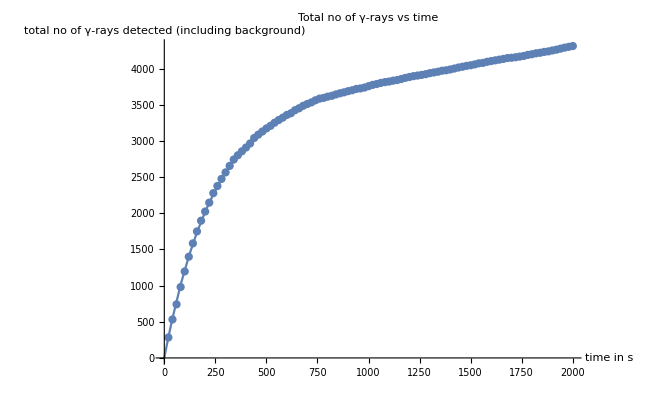

```mathematica
Show[%8,AxesLabel->{HoldForm[time in s],HoldForm[total no of γ-rays detected(including background)]},PlotLabel->HoldForm[Total no of γ-rays vs time],LabelStyle->{GrayLevel[0]}]
```

```mathematica
note:λ and c are divided by 20 because data given is not in 1 s intervals but in 20 s intervals.
```

```mathematica
error1=Table[9.952658590343818*t+∫_0^t 0.0869922*3306.43*ⅇ^(-0.08699216923625656*x)ⅆx-decay[[t]],{t,1,100}]
```

{2.43037,15.9091,48.3485,31.5013,19.9746,5.24123,-6.3485,-11.5568,-12.2491,-3.38518,-1.01167,-16.2545,-8.31257,-7.45134,-5.9976,-11.3342,-20.8953,-7.16247,5.33982,16.0473,18.3595,-3.35741,1.23225,5.43621,6.53655,11.7918,7.43915,6.69573,7.76078,2.81689,9.03144,-4.44215,-4.46322,-12.9029,-13.6428,-12.5749,-19.5996,-21.626,-11.5706,-9.35698,-2.91491,-4.18014,-3.09374,0.398305,0.345517,2.79329,-0.21677,7.35349,9.53903,4.3719,-0.118511,1.09473,-0.963685,0.728875,5.19316,5.44818,8.51138,6.39874,2.12491,1.70332,1.14628,4.46507,6.67004,7.77068,4.77567,5.69298,6.52992,3.29319,7.98892,7.62274,5.19982,1.72486,1.20222,-0.364137,2.02943,0.386266,-4.29057,0.00171743,-4.73429,-4.49623,-4.28196,-4.08947,-3.91698,-5.76279,0.374601,3.4966,4.6045,5.69946,0.782559,1.85479,-1.08293,1.97021,0.0149757,3.05207,0.0821294,-0.89426,-4.87656,-8.86428,-9.85697,-10.8542}

```mathematica
ListPlot[Transpose[{20*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},error1}]]
```

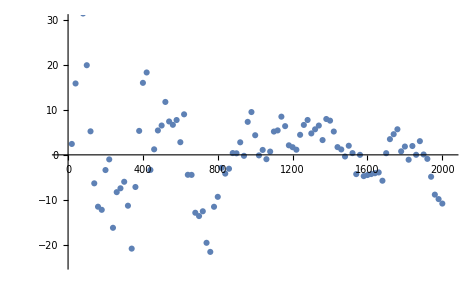

```mathematica
Plot[c+λ*N*ⅇ^(-λ*t)/.{λ->0.08699216923625656/20,N->3306.4299611548245,c->9.952658590343818/20},{t,0,2000}]
```

```mathematica
Show[%36,AxesLabel->{HoldForm[time in s],HoldForm[decay rate including background]},PlotLabel->None]
```

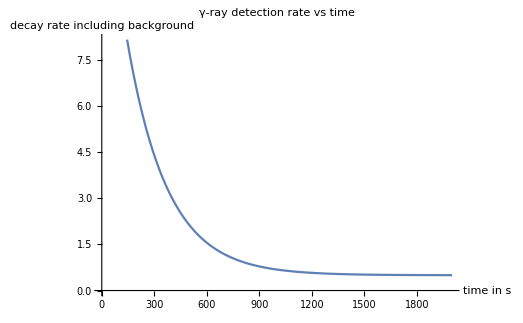

```mathematica
Show[%37,PlotLabel->HoldForm[ γ-ray detection rate vs time]]
```

```mathematica
note:if we find the area under this curve from 0 to 20, 20to 40 etc, we get back the original data.
```

```mathematica
N[Log[2]]/(0.08699216923625656/20)
```

159.359

```mathematica
Barium  decay constant is λ=0.08699216923625656/20

the decay rate of barium(excluding background) is λ*N*ⅇ^(-λ*t),which will become half of its initial value at
λ*N/2=λ*N*ⅇ^(-λ*t)
```

which implies
t=ln2/λ

```mathematica
Thus half-life of^(137m)Ba is 159.359 s.
```

```mathematica
atoms=Table[3306-(decay[[n]]-10*n), {n,1,100}]
```

{3033,2794,2595,2366,2160,1967,1792,1637,1499,1382,1269,1148,1059,971,891,811,733,684,639,597,551,485,449,416,383,357,324,297,274,247,233,201,184,160,145,133,114,101,101,94,92,83,77,74,68,65,57,60,58,49,41,39,34,33,35,33,34,30,24,22,20,22,23,23,19,19,19,15,19,18,15,11,10,8,10,8,3,7,2,2,2,2,2,0,6,9,10,11,6,7,4,7,5,8,5,4,0,-4,-5,-6}

```mathematica
dataNo=Transpose[{20*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},atoms}]
```

{{20,3033},{40,2794},{60,2595},{80,2366},{100,2160},{120,1967},{140,1792},{160,1637},{180,1499},{200,1382},{220,1269},{240,1148},{260,1059},{280,971},{300,891},{320,811},{340,733},{360,684},{380,639},{400,597},{420,551},{440,485},{460,449},{480,416},{500,383},{520,357},{540,324},{560,297},{580,274},{600,247},{620,233},{640,201},{660,184},{680,160},{700,145},{720,133},{740,114},{760,101},{780,101},{800,94},{820,92},{840,83},{860,77},{880,74},{900,68},{920,65},{940,57},{960,60},{980,58},{1000,49},{1020,41},{1040,39},{1060,34},{1080,33},{1100,35},{1120,33},{1140,34},{1160,30},{1180,24},{1200,22},{1220,20},{1240,22},{1260,23},{1280,23},{1300,19},{1320,19},{1340,19},{1360,15},{1380,19},{1400,18},{1420,15},{1440,11},{1460,10},{1480,8},{1500,10},{1520,8},{1540,3},{1560,7},{1580,2},{1600,2},{1620,2},{1640,2},{1660,2},{1680,0},{1700,6},{1720,9},{1740,10},{1760,11},{1780,6},{1800,7},{1820,4},{1840,7},{1860,5},{1880,8},{1900,5},{1920,4},{1940,0},{1960,-4},{1980,-5},{2000,-6}}

```mathematica
Show[ListPlot[dataNo],Plot[N*ⅇ^(-λ*t)/.{λ->0.08699216923625656/20,N->3306.4299611548245},{t,0,2000}]]
```

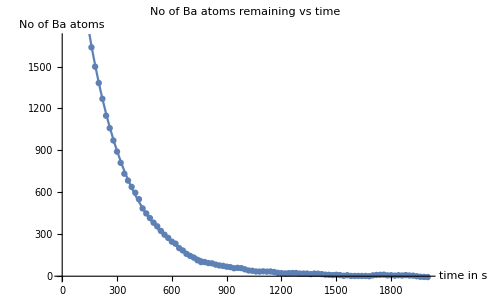

```mathematica
Show[%52,AxesLabel->{HoldForm[time in s],HoldForm[No of Ba atoms]},PlotLabel->HoldForm[No of Ba atoms remaining vs time],LabelStyle->{GrayLevel[0]}]
```

```mathematica
error2=Table[3306.4299611548245*ⅇ^(-0.08699216923625656*(t))-atoms[[t]], {t, 1, 100}]
```

{-2.04765,-15.5736,-48.0603,-31.2604,-19.7809,-5.09482,6.44762,11.6087,12.2536,3.34243,0.921623,16.1172,8.12791,7.21938,5.71832,11.0076,20.5214,6.74124,-5.80837,-16.5632,-18.9227,2.74689,-1.8901,-6.14138,-7.28905,-12.5917,-8.28631,-7.59023,-8.70261,-3.80606,-10.0679,3.35832,3.33206,11.7243,12.417,11.3017,18.2791,20.2582,10.1555,7.89446,1.40505,2.62294,1.4892,-2.05018,-2.04474,-4.53985,-1.57713,-9.19472,-11.4276,-6.30782,-1.86475,-3.12533,-1.11425,-2.85415,-7.36578,-7.66814,-10.7787,-8.71338,-4.48689,-4.11264,-3.60294,-6.96907,-9.22139,-10.3694,-7.42169,-8.38635,-9.27063,-6.08124,-10.8243,-10.5055,-8.12989,-4.70228,-4.22698,-2.70796,-5.14887,-3.55305,1.07645,-3.26318,1.42548,1.14009,0.878469,0.638647,0.418807,2.21728,-3.96745,-7.1368,-8.29203,-9.43433,-4.56478,-5.68435,-2.79397,-5.89445,-3.98656,-7.07099,-4.14839,-3.21935,0.715613,4.65599,5.60134,6.55124}

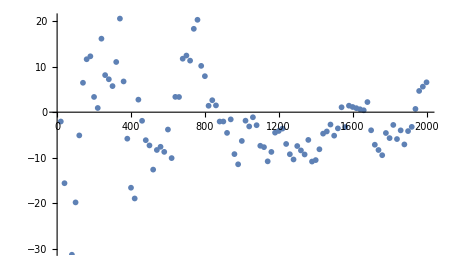

```mathematica
ListPlot[Transpose[{20*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},error2}]]
```